```mathematica
dir=NotebookDirectory[];
a=SetDirectory[dir]
date = DateString[Riffle[{"Month","Day"},"_"]]
```

D:\Curve Elasticity\Simulation\2026\jan\results\helicoidC\st rad - Copy

09_23

```mathematica
gb=1
X[u_,v_]:={u Cos[v], u Sin[v],v};
uu=Import["uu_2_26_"<>date<>".txt","Table"];
vv=Import["vv_2_26_"<>date<>".txt","Table"];
uu=Flatten[uu];
vv=Flatten[vv];
points=MapThread[X,{uu,vv}];
V2k=Graphics3D[{Yellow,Thickness[0.01],Line[points]},Boxed->False];

V3=ParametricPlot3D[X[u,v],{u,-Pi,5},{v,0,2Pi},PlotStyle->Directive[LightRed]];

Show[ V3,V2k,PlotRange->All]
```

1

-Graphics3D-

```mathematica
Show[%383,Boxed->False]
```

-Graphics3D-

```mathematica
X[u_,v_]:={u Cos[v],u Sin[v],c v};
(*First derivatives*)
Xu=D[X[u,v],u]
Xv=D[X[u,v],v]

(*Second derivatives*)
Xuu=D[X[u,v],{u,2}];
Xuv=D[Xu,v];
Xvv=D[X[u,v],{v,2}];

(*Normal vector to surface*)
nVec=Cross[Xu,Xv]//Simplify ;
n2=Sqrt[nVec.nVec]  //FullSimplify ;
nVec=nVec/n2 //FullSimplify;

(*First fundamental form:g_ij= <X_i,X_j>*)
g11=Simplify[Xu.Xu];
g12=Simplify[Xu.Xv];
g22=Simplify[Xv.Xv];
gMat={{g11,g12},{g12,g22}}


(*Second fundamental form:b_ij= <X_ij,n>*)
b11=Simplify[Xuu.nVec];
b12=Simplify[Xuv.nVec];
b22=Simplify[Xvv.nVec];
bMat={{b11,b12},{b12,b22}};
```

{Cos[v],Sin[v],0}

{-u Sin[v],u Cos[v],c}

{{1,0},{0,c^2+u^2}}

```mathematica
ChristoffelSymbol[g_,xx_]:=Block[{n,ig,res},n=Length[xx];ig=Inverse[g];res=Table[(1/2)*Sum[ig[[i,s]]*(-D[g[[j,k]],xx[[s]]]+D[g[[j,s]],xx[[k]]]+D[g[[s,k]],xx[[j]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}];Simplify[res]];

(*The coordinates*)xx={u,v};
CS=ChristoffelSymbol[gMat,xx]
```

{{{0,0},{0,-u}},{{0,u/(c^2+u^2)},{u/(c^2+u^2),0}}}

```mathematica
kG = Det[Inverse[gMat].bMat]
H = 1/2Tr[Inverse[gMat].bMat]
```

-c^2/((c^2+u^2)^2)

0

```mathematica
u0=1;
v0=x;
c=1;
R=1;
```

```mathematica
X[u_,v_]:={u Cos[v],u Sin[v],c v};
NN= nVec /.{u->u0, v->v0};
X0 = X[u0,v0];
X01 = D[X0,x] ;
g1=Sqrt[X01.X01] //Simplify;
Xs=X01/g1;
Xss = D[Xs,x]/g1;
nn=Cross[NN,Xs] //Simplify;

ns=D[nn,x]/g1;
kg=Xss.nn  //Simplify  
kn = Xss.NN //Simplify   //N
taug = ns.NN //Simplify   //N
```

1/2

0.

0.5

```mathematica
NN
```

{Sin[x]/(√2),-Cos[x]/(√2),1/(√2)}

```mathematica
nn
```

{-Cos[x],-Sin[x],0}

Import::nffil: File D:\Curve Elasticity\Simulation\oct\oct13\cylinder\helix\l1_2_25_10_14.txt not found during Import.

Import::nffil: File D:\Curve Elasticity\Simulation\oct\oct13\cylinder\helix\l2_2_25_10_14.txt not found during Import.

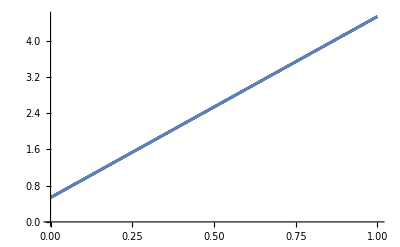

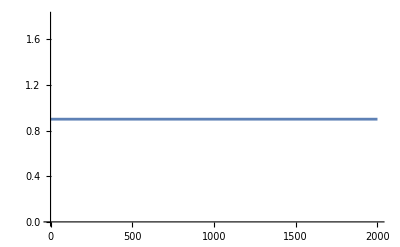

```mathematica
l1=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\cylinder\\helix\\l1_2_25_10_14.txt","Table"];
l2=Import["D:\\Curve Elasticity\\Simulation\\oct\\oct13\\cylinder\\helix\\l2_2_25_10_14.txt","Table"];

ListLinePlot[Transpose[Reverse[uu]],DataRange->{0,1}]
ListLinePlot[Transpose[vv]]
```

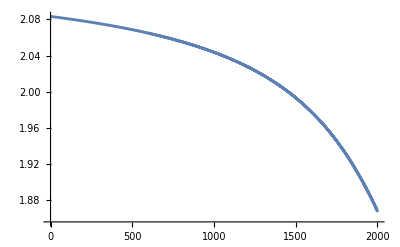

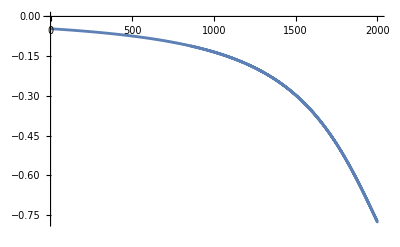

```mathematica
tg=Import["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\st rad - Copy\\taug_2_26_09_23.txt","Table"];
phi=Import["D:\\Curve Elasticity\\Simulation\\2026\\jan\\results\\helicoidC\\st rad - Copy\\phi_2_26_09_23.txt","Table"];
ListLinePlot[Transpose[phi]]
ListLinePlot[Transpose[tg]]
```

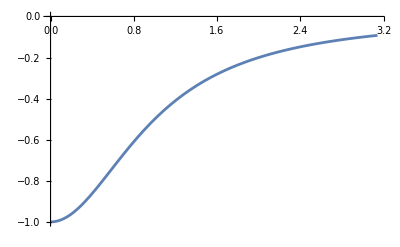

```mathematica
Plot[-1/(1+x^2),{x,0,Pi}]
```

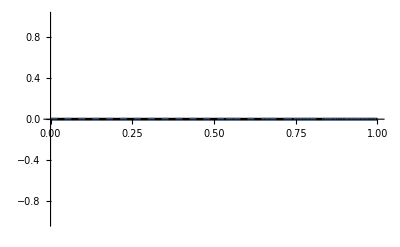

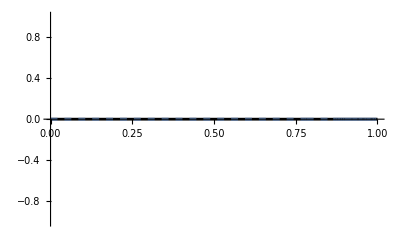

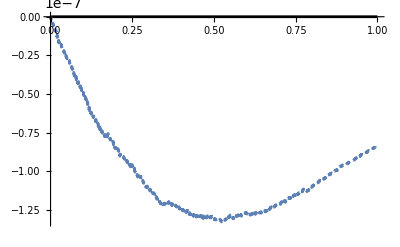

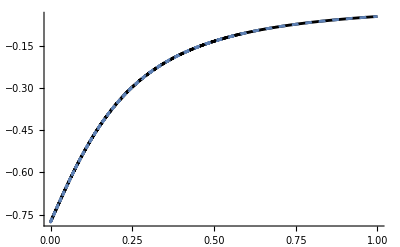

```mathematica
kn1x=Import["kn1_2_26_"<>date<>".txt","Table"];
kn2x=Import["kn2_2_26_"<>date<>".txt","Table"];
kn1xs=Import["kn1s_.txt","Table"];
kn2xs=Import["kn2s_.txt","Table"] ;

taugx=Import["taug_2_26_"<>date<>".txt","Table"];
taugxs=Import["taugs_.txt","Table"] ;

kgx=Import["kg_2_26_"<>date<>".txt","Table"];
kgxs=Import["kgs_.txt","Table"] ;


a1=ListLinePlot[Transpose[kn1x],DataRange->{0,1},PlotStyle->{Black}];
a1s=ListLinePlot[Transpose[kn1xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a1,a1s]

a2=ListLinePlot[Transpose[kn2x],DataRange->{0,1},PlotStyle->{Black}];
a2s=ListLinePlot[Transpose[kn2xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a2,a2s]

a3=ListLinePlot[Transpose[kgx],DataRange->{0,1},PlotStyle->{Black}];
a3s=ListLinePlot[Transpose[kgxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a3,a3s, PlotRange->All]

a4=ListLinePlot[Transpose[Reverse[taugx]],DataRange->{0,1},PlotStyle->{Black}];
a4s=ListLinePlot[Transpose[Reverse[taugxs]],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
Show[a4,a4s, PlotRange ->All]
```

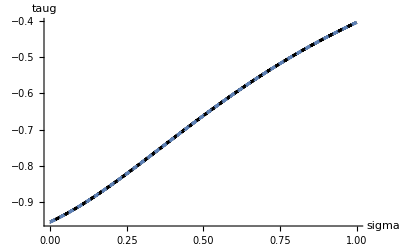

```mathematica
Show[%162,AxesLabel->{HoldForm[sigma],HoldForm[taug]},PlotLabel->None,LabelStyle->{GrayLevel[0]},PlotLegends->Automatic]
```

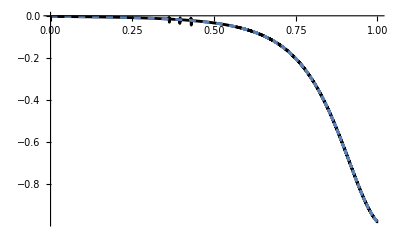

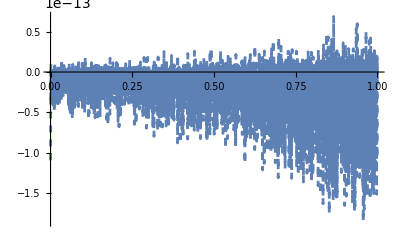

```mathematica
aG=ListLinePlot[Transpose[kn1x*kn2x - taugx*taugx],DataRange->{0,1},PlotStyle->Black];
aH=ListLinePlot[0.5*Transpose[kn1x+kn2x],DataRange->{0,1},PlotStyle->Black];

aGs=ListLinePlot[Transpose[kn1xs*kn2xs - taugxs*taugxs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];
aHs=ListLinePlot[0.5*Transpose[kn1xs+kn2xs],DataRange->{0,1},PlotStyle->{Dashed,Yellow}];

Show[aG,aGs,PlotRange->All]
Show[aH,aHs,PlotRange->All]
```